# Harmonic Spectrum Calculation

We present a method to numerically calculate the harmonic spectrum for a single-active electron in a two-level system. This is a model system for a transparent semiconductor being irradiated with a high-intensity infrared laser pulse. We begin by numerically solving the time-dependent Schrödinger equation (TDSE) to find the time-dependent coefficients of the wave function. We then take the Fourier transform of the expectation value of the dipole operator in order to calculate the harmonic spectrum.

```mathematica
(*define default plot settings and Fourier function*)
SetOptions[ListPlot,Joined->True,Axes->False,Frame->True,ImageSize->Medium];
fourier[ls_, dt_,
  t0 : (_?(NumberQ[#] && ! MatchQ[#, _Complex] &)) : 0.,
  withW : (True | False) : True] := Module[{N0, dw, wls, fft, phase},
  N0 = Length[ls];
  dw = (2 π)/(N0 dt);
  If[EvenQ[N0],
    wls = dw Range[-(N0/2), N0/2 - 1];
    fft = (Sqrt[N0]*dt)/Sqrt[2 π]*RotateRight[Fourier[ls], N0/2];,
    wls = dw Range[-((N0 - 1)/2), (N0 - 1)/2];
    fft = (Sqrt[N0]*dt)/Sqrt[2 π]*
        RotateRight[Fourier[ls], (N0 - 1)/2];
  ];
  phase = Exp[I wls t0];
  If[withW, Transpose[{wls, fft*phase}], fft*phase]
];
```

```mathematica
(*define parameters*)
ω0=1.;
ω=0.1;T=2π/ω;
Ω0=1;n=11;
μ=1;
t0=2π*n/ω;
dt=t0/1000/n;
ω21=10ω;
E0=1;

(*define incoming laser pulse*)
ϵ[t_]=E0*Sin[(ω*t)/(2*n)]^2*Sin[ω*t];

(*solve TDSE for coefficients*)
sol=NDSolve[{C1'[t]==I*μ*ϵ[t]*Exp[-I*(ω21)*t]*C2[t],C2'[t]==I*μ*ϵ[t]*Exp[I*(ω21)*t]*C1[t],C1[0]==1,C2[0]==0},{C1,C2},{t,0,t0}];
c1[t_]:=C1[t]/.sol;
c2[t_]=C2[t]/.sol;
```

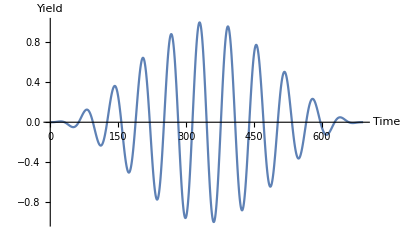

```mathematica
(*plot of incoming laser pulse*)
LaserPulse=Plot[ϵ[t],{t,0,t0},AxesLabel->{"Time","Yield"}]
```

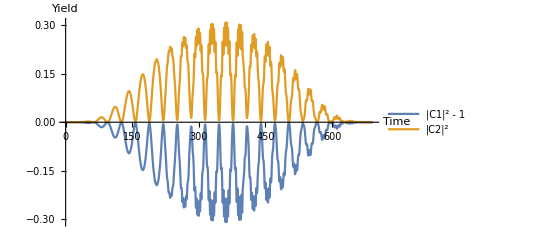

```mathematica
(*plot of solutions to TDSE*)
CoeffPlot=Plot[{Abs[c1[t]]^2-1,Abs[c2[t]]^2},{t,0,t0},PlotRange->All,PlotLegends->{"|C1|^2 - 1","|C2|^2"},AxesLabel->{"Time","Yield"}]
```

```mathematica
(*calculate time dependent dipole moment*)
term[t_]:=μ*Conjugate[c1[t]]*c2[t]*Exp[-I*ω21*t];
d[t_]:=term[t]+Conjugate[term[t]];
```

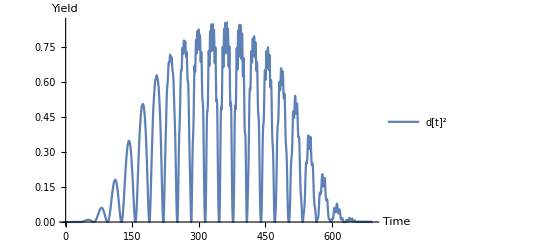

```mathematica
(*plot of time-dependent dipole moment*)
DipolePlot=Plot[d[t]^2,{t,0,t0},AxesLabel->{"Time","Yield"},PlotLegends->{"d[t]^2"}]
```

```mathematica
(*calculate Fourier transform of dipole*)
dlist=Flatten[Table[d[ti],{ti,0,t0,dt}]];
{w,data}=Transpose[fourier[dlist,dt]];
```

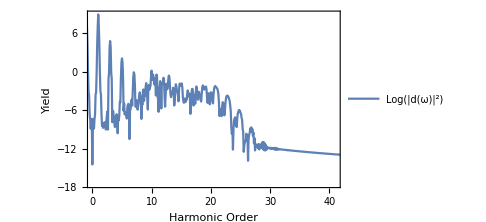

```mathematica
(*plot harmonic spectrum*)
HarmSpec=ListPlot[Log[Abs[data]^2],DataRange->{w[[1]]/ω,w[[Length[w]]]/ω},PlotRange->{{0,41},All},FrameLabel->{"Harmonic Order","Yield"},PlotLegends->{"Log(|d(ω)|^2)"}]
```